## Compare to Alice Data

```mathematica
Alicedatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*Alicedata=ImportString[StringReplace[StringReplace[Alicedatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
Alicedata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[Alicedata];
titles=Alicedata[[1]];
enumeratedtitles=Transpose[{Range[Length[titles]],titles}]
πplus=Alicedata[[2;;42]];
πminus=Alicedata[[44;;]];
aliceps=(Transpose@πplus)[[1]];
aliceyieldplus=(Transpose@πplus)[[4]];
aliceyieldminus=(Transpose@πminus)[[4]];
```

{{1,PT [GEV]},{2,PT [GEV] LOW},{3,PT [GEV] HIGH},{4,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2]},{5,stat +},{6,stat -},{7,sys +},{8,sys -},{9,sys,normalization uncertainty +},{10,sys,normalization uncertainty -}}

```mathematica
Fluidumdata=Import[StringJoin[NotebookDirectory[],"data/pionSpectra.txt"],"CSV"];
```

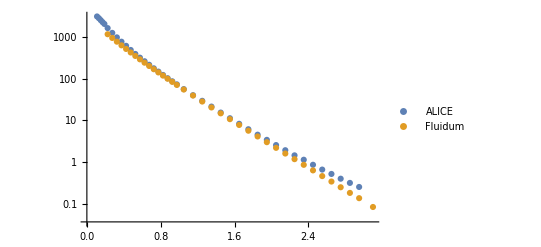

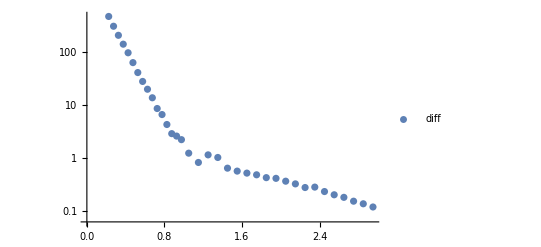

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListFluidum=Transpose@{Fluidumdata[[1]],2*Fluidumdata[[2]]};
ListLogPlot[
{ListALICE,
ListFluidum},
PlotLegends->{"ALICE","Fluidum"}
]

diff=(Transpose@ListALICE)[[2]][[6;;]]-(Transpose@ListFluidum)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICE)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```

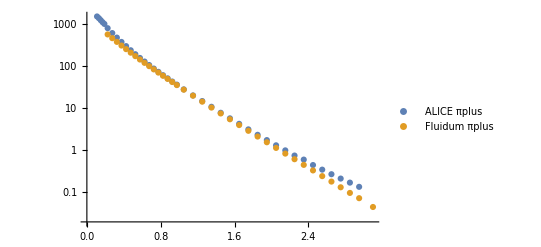

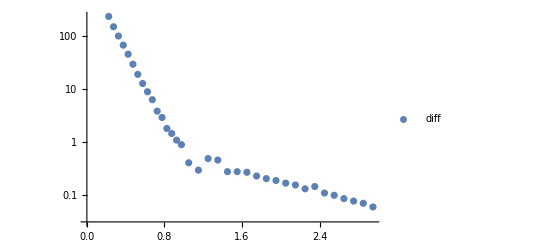

```mathematica
ListALICEπplus=Transpose@{aliceps,aliceyieldplus};
ListFluidumπplus=Transpose@{Fluidumdata[[1]],Fluidumdata[[2]]};
ListLogPlot[
{ListALICEπplus,
ListFluidumπplus},
PlotLegends->{"ALICE πplus","Fluidum πplus"}
]

diff=(Transpose@ListALICEπplus)[[2]][[6;;]]-(Transpose@ListFluidumπplus)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICEπplus)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```

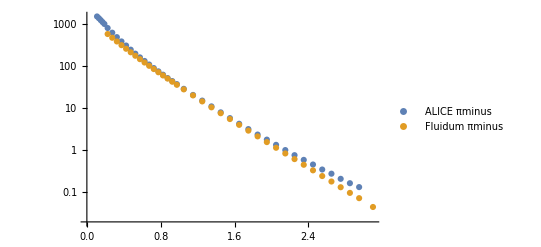

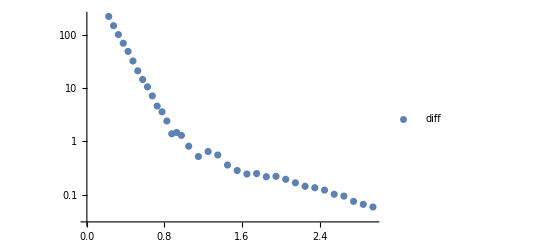

```mathematica
ListALICEπminus=Transpose@{aliceps,aliceyieldminus};
ListFluidumπminus=Transpose@{Fluidumdata[[1]],Fluidumdata[[2]]};
ListLogPlot[
{ListALICEπminus,
ListFluidumπminus},
PlotLegends->{"ALICE πminus","Fluidum πminus"}
]

diff=(Transpose@ListALICEπminus)[[2]][[6;;]]-(Transpose@ListFluidumπminus)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICEπminus)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```